```mathematica
Manipulate[Plot[{(Sign[x+Pi-2 Pi*(IntegerPart[(x+Pi)/(2 Pi)]+(Sign[(x+Pi)]-1)/2)-Pi]) Pi/4,Sum[Sin[(2 k-1) x]/(2 k-1),{k,1,m}]},{x,-2 Pi,2 Pi},AspectRatio->Automatic,PlotRange->{-1,1},PlotStyle->{{Thickness[0.002],RGBColor[1,0,0]},{Thickness[0.004],RGBColor[0,1,0]}}],{m,1,9}]
```

```mathematica
Manipulate[Plot[{Pi/2+2/Pi*Sum[{(((-1)^k-1)/(k^2))*Cos[k*x]},{k,1,n}],Abs[x-Round[x/(2 Pi)]*2 Pi]},{x,-10,10},AspectRatio->Automatic,PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.002],RGBColor[1,0,0]}},AxesOrigin->{0,0}],{n,1,8}]
```

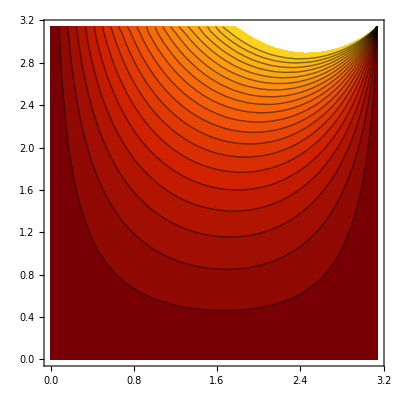

```mathematica
ContourPlot[-2*Sum[(-1)^n/n*Sin[n*x]*Sinh[n*y]/Sinh[n*Pi],{n,1,100}],{x,0,Pi},{y,0,Pi},ColorFunction->"SolarColors",Contours->20]
```